```mathematica
X[J_,μ_]:= 1/2(J+μ);
B[J_]:= Exp[-J];
```

```mathematica
λp[J_,μ_]:= Exp[X[J,μ]](Cosh[X[J,μ]]+√((Sinh[X[J,μ]])^2+B[J]));
λm[J_,μ_]:= Exp[X[J,μ]](Cosh[X[J,μ]]-√((Sinh[X[J,μ]])^2+B[J]));
```

```mathematica
vm[J_,μ_]:= Exp[-μ/2](λm[J,μ]-1);
```

```mathematica
ϕav[J_,μ_,Nm_]:=(λp[J,μ]^Nm+λm[J,μ]^Nm vm[J,μ]^2)/((λp[J,μ]^Nm+λm[J,μ]^Nm)(1+vm[J,μ]^2));
```

```mathematica
ϕav2[J_,μ_,Nm_]:= (λp[J,μ]^Nm(1+vm[J,μ]^2)+λm[J,μ]^Nm(vm[J,μ]^2+vm[J,μ]^4))/((λp[J,μ]^Nm+λm[J,μ]^Nm)(1+vm[J,μ]^2)^2);
```

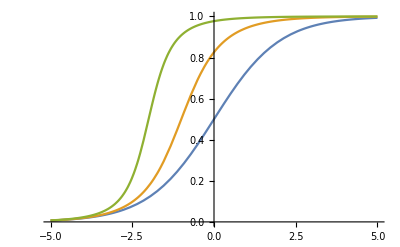

```mathematica
Plot[{ϕav2[0,μ,12],ϕav2[1,μ,12],ϕav2[2,μ,12]},{μ,-5,5}]
```

```mathematica
ϕvar[J_,μ_,Nm_]:= Sqrt[ϕav2[J,μ,Nm]-ϕav[J,μ,Nm]^2];
```

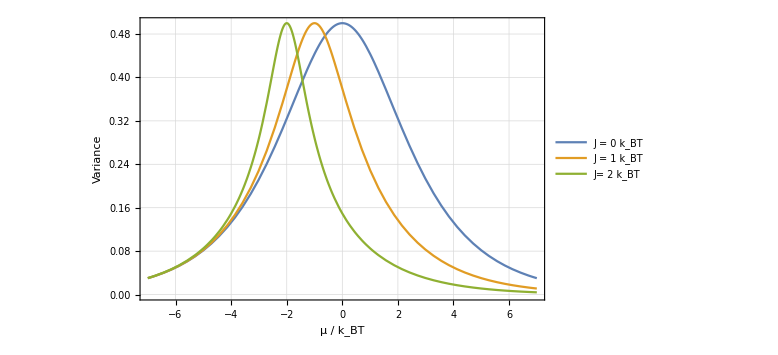

```mathematica
Plot[{ϕvar[0,μ,12],ϕvar[1,μ,12],ϕvar[2,μ,12]},{μ,-7,7}, Frame->True,FrameLabel->{"μ / k_BT", "Variance"},ImageSize->Large,LabelStyle->{GrayLevel[0],12}, GridLines->Automatic,PlotLegends->Placed[LineLegend[{"J = 0 k_BT","J = 1 k_BT","J= 2 k_BT"},LegendFunction->Frame],{{0.9,0.5},{0.7,0.5}}]]
```

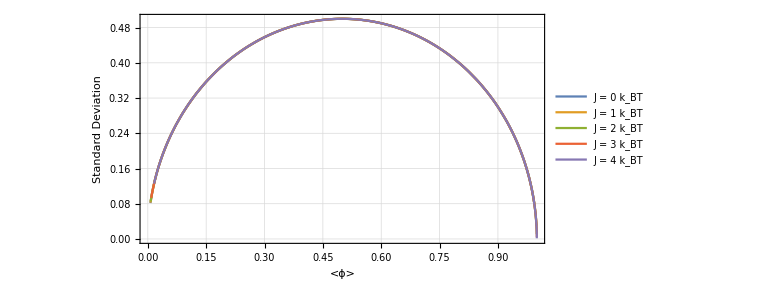

```mathematica
ParametricPlot[{{ϕav[0,μ,12],ϕvar[0,μ,12]},{ϕav[1,μ,12],ϕvar[1,μ,12]},{ϕav[2,μ,12],ϕvar[2,μ,12]},{ϕav[3,μ,12],ϕvar[3,μ,12]},{ϕav[4,μ,12],ϕvar[4,μ,12]}},{μ,-5,5},ImageSize->Large,Frame->True,GridLines->Automatic,FrameLabel->{"<ϕ>","Standard Deviation"},LabelStyle->{GrayLevel[0],12},PlotLegends->Placed[LineLegend[{"J = 0 k_BT","J = 1 k_BT","J = 2 k_BT","J = 3 k_BT","J = 4 k_BT"},LegendFunction->Frame],{{0.5,0.1},{0.5,0}}]]
```